```mathematica
PHY 206 Project 

Adarsh Kumar (19011)
Arihant Tiwari (19050)
Abhisek Swain (19007)
Gourav Kumawat (19127) 
Rita Abani (19244)             
Yatharth Pal  (19340)


Problem 1
```

```mathematica
ClearAll;
```

```mathematica
ImprovedCoupledDiffEqn1stOrderSolver[dθ1_, dθ2_, dω1_,dω2_,θ1i_, θ2i_,ω1i_,ω2i_, ti_, tf_, 
  h_] := 
 Module[{tstep, Datapoints}, tstep = (tf - ti)/h//N;    
                   
  For[Datapoints = {{ti, θ1i, θ2i,ω1i,ω2i}}, Length[Datapoints] ≤ h,    
                          AppendTo[Datapoints , new],
                          prev = Last[Datapoints];    
                         incre =  tstep {1, dθ1 @@ prev, dθ2 @@ prev,dω1@@prev,dω2@@prev} ;
                          prevP = prev +    incre ;
                          
   increP = tstep {1, dθ1 @@ prevP, dθ2 @@ prevP,dω1@@prevP,dω2@@prevP} ;
                          avgincre = (incre + increP)/2;
                          new = prev + avgincre;
                         ];
        Return[Datapoints];      
  ]
```

```mathematica
Part A : Solving  θA and θB as a function of time, when there is a driving force and no viscous force
```

```mathematica
ω = 0.02;
x = 0.1;
θAi = 0;
θBi = 0;
ωAi = 0;
ωBi = 0;
t1 = 0;
t2 = 100;
stepsize =10000;
dθA[t_,θA_,θB_,ωA_,ωB_] = ωA;
dθB[t_,θA_,θB_,ωA_,ωB_] = ωB;
dωA[t_,θA_,θB_,ωA_,ωB_] = -Sin[θA] + x*(1 - 2/(Sqrt[(2+Sin[θB]-Sin[θA])^2  + (Cos[θA]-Cos[θB])^2]))*(2Cos[θA]-Sin[θA-θB]);
dωB[t_,θA_,θB_,ωA_,ωB_] =-Sin[θB] + (1/2)Cos[ω*t] + x*(1 - 2/(Sqrt[(2+Sin[θB]-Sin[θA])^2  + (Cos[θA]-Cos[θB])^2]))*(-2Cos[θB]+Sin[θA-θB]);
```

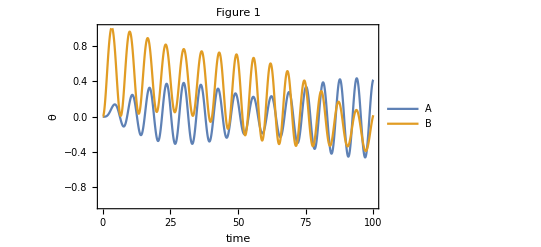

```mathematica
A = ImprovedCoupledDiffEqn1stOrderSolver[dθA, dθB, dωA, dωB ,θAi, θBi,ωAi,ωBi,t1,t2,stepsize];
ListLinePlot[ {A[[;;,{1,2}]],A[[;;,{1,3}]]}, PlotRange -> {{0,100},{-1,1}}, AxesLabel -> {"time", "θ"},PlotLegends ->{"A","B"}, PlotLabel -> "Figure 1",Frame->True]
```

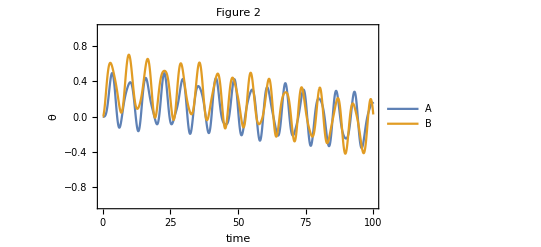

```mathematica
ω = 0.02;
x = 1;
dθA[t_,θA_,θB_,ωA_,ωB_] = ωA;
dθB[t_,θA_,θB_,ωA_,ωB_] = ωB;
dωA[t_,θA_,θB_,ωA_,ωB_] = -Sin[θA] + x*(1 - 2/(Sqrt[(2+Sin[θB]-Sin[θA])^2  + (Cos[θA]-Cos[θB])^2]))*(2Cos[θA]-Sin[θA-θB]);
dωB[t_,θA_,θB_,ωA_,ωB_] =-Sin[θB] + (1/2)Cos[ω*t] + x*(1 - 2/(Sqrt[(2+Sin[θB]-Sin[θA])^2  + (Cos[θA]-Cos[θB])^2]))*(-2Cos[θB]+Sin[θA-θB]);
A = ImprovedCoupledDiffEqn1stOrderSolver[dθA, dθB, dωA, dωB ,θAi, θBi,ωAi,ωBi,t1,t2,stepsize];
ListLinePlot[ {A[[;;,{1,2}]],A[[;;,{1,3}]]}, PlotRange -> {{0,100},{-1,1}}, AxesLabel -> {"time", "θ"},PlotLegends ->{"A","B"}, PlotLabel -> "Figure 2",Frame->True]
```

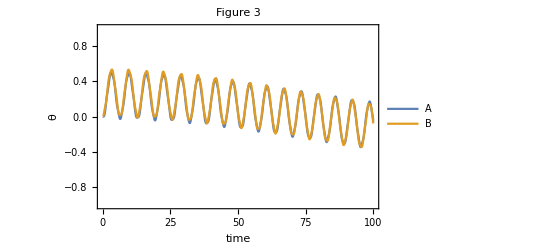

```mathematica
ω = 0.02;
x = 10;
dθA[t_,θA_,θB_,ωA_,ωB_] = ωA;
dθB[t_,θA_,θB_,ωA_,ωB_] = ωB;
dωA[t_,θA_,θB_,ωA_,ωB_] = -Sin[θA] + x*(1 - 2/(Sqrt[(2+Sin[θB]-Sin[θA])^2  + (Cos[θA]-Cos[θB])^2]))*(2Cos[θA]-Sin[θA-θB]);
dωB[t_,θA_,θB_,ωA_,ωB_] =-Sin[θB] + (1/2)Cos[ω*t] + x*(1 - 2/(Sqrt[(2+Sin[θB]-Sin[θA])^2  + (Cos[θA]-Cos[θB])^2]))*(-2Cos[θB]+Sin[θA-θB]);
A = ImprovedCoupledDiffEqn1stOrderSolver[dθA, dθB, dωA, dωB ,θAi, θBi,ωAi,ωBi,t1,t2,stepsize];
ListLinePlot[ {A[[;;,{1,2}]],A[[;;,{1,3}]]}, PlotRange ->{{0,100},{-1,1}}, AxesLabel -> {"time", "θ"},PlotLegends ->{"A","B"}, PlotLabel -> "Figure 3",Frame->True]
```

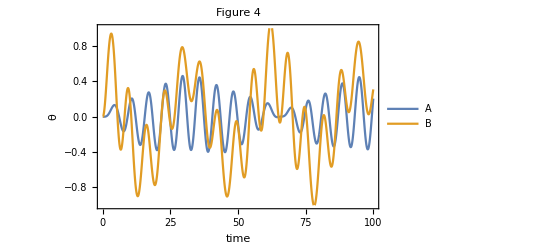

```mathematica
ω = 0.2;
x = 0.1;
dθA[t_,θA_,θB_,ωA_,ωB_] = ωA;
dθB[t_,θA_,θB_,ωA_,ωB_] = ωB;
dωA[t_,θA_,θB_,ωA_,ωB_] = -Sin[θA] + x*(1 - 2/(Sqrt[(2+Sin[θB]-Sin[θA])^2  + (Cos[θA]-Cos[θB])^2]))*(2Cos[θA]-Sin[θA-θB]);
dωB[t_,θA_,θB_,ωA_,ωB_] =-Sin[θB] + (1/2)Cos[ω*t] + x*(1 - 2/(Sqrt[(2+Sin[θB]-Sin[θA])^2  + (Cos[θA]-Cos[θB])^2]))*(-2Cos[θB]+Sin[θA-θB]);
A = ImprovedCoupledDiffEqn1stOrderSolver[dθA, dθB, dωA, dωB ,θAi, θBi,ωAi,ωBi,t1,t2,stepsize];
ListLinePlot[ {A[[;;,{1,2}]],A[[;;,{1,3}]]}, PlotRange -> {{0,100},{-1,1}}, AxesLabel -> {"time", "θ"},PlotLegends ->{"A","B"}, PlotLabel -> "Figure 4",Frame->True]
```

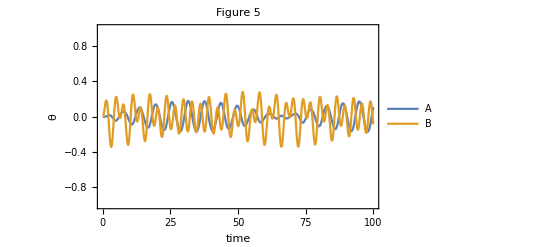

```mathematica
ω = 2;
x = 0.1;
dθA[t_,θA_,θB_,ωA_,ωB_] = ωA;
dθB[t_,θA_,θB_,ωA_,ωB_] = ωB;
dωA[t_,θA_,θB_,ωA_,ωB_] = -Sin[θA] + x*(1 - 2/(Sqrt[(2+Sin[θB]-Sin[θA])^2  + (Cos[θA]-Cos[θB])^2]))*(2Cos[θA]-Sin[θA-θB]);
dωB[t_,θA_,θB_,ωA_,ωB_] =-Sin[θB] + (1/2)Cos[ω*t] + x*(1 - 2/(Sqrt[(2+Sin[θB]-Sin[θA])^2  + (Cos[θA]-Cos[θB])^2]))*(-2Cos[θB]+Sin[θA-θB]);
A = ImprovedCoupledDiffEqn1stOrderSolver[dθA, dθB, dωA, dωB ,θAi, θBi,ωAi,ωBi,t1,t2,stepsize];
ListLinePlot[ {A[[;;,{1,2}]],A[[;;,{1,3}]]}, PlotRange -> {{0,100},{-1,1}}, AxesLabel -> {"time", "θ"},PlotLegends ->{"A","B"}, PlotLabel -> "Figure 5",Frame->True]
```

```mathematica
Part B : Driving Force = 0. Including Viscous force = -γv=-γωL
```

```mathematica
γ = 0.14;
x = 0.1;
θAi = 0;
θBi = 0;
ωAi = 0;
ωBi = 0;
t1 = 0;
t2 = 50;
L = 2;
stepsize =10000;
dθA[t_,θA_,θB_,ωA_,ωB_] = ωA;
dθB[t_,θA_,θB_,ωA_,ωB_] = ωB;
dωA[t_,θA_,θB_,ωA_,ωB_] = -Sin[θA] + x*(1 - 2/(Sqrt[(2+Sin[θB]-Sin[θA])^2  + (Cos[θA]-Cos[θB])^2]))*(2Cos[θA]-Sin[θA-θB])-γ*(ωA*L);
dωB[t_,θA_,θB_,ωA_,ωB_] =-Sin[θB]  + x*(1 - 2/(Sqrt[(2+Sin[θB]-Sin[θA])^2  + (Cos[θA]-Cos[θB])^2]))*(-2Cos[θB]+Sin[θA-θB])-γ*(ωB*L);
```

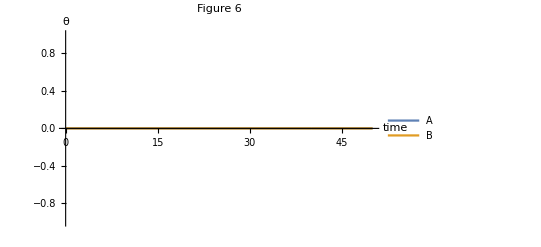

```mathematica
A = ImprovedCoupledDiffEqn1stOrderSolver[dθA, dθB, dωA, dωB ,θAi, θBi,ωAi,ωBi,t1,t2,stepsize];
ListLinePlot[ {A[[;;,{1,2}]],A[[;;,{1,3}]]}, PlotRange -> Full, AxesLabel -> {"time", "θ"},PlotLegends ->{"A","B"},PlotLabel -> "Figure 6"]
```

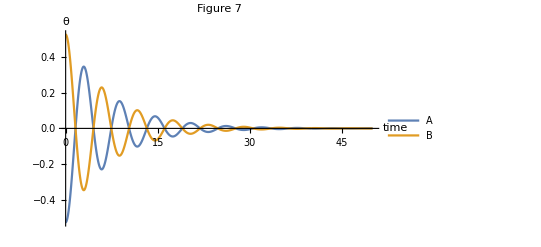

```mathematica
θBi = 3.14/6;θAi = -3.14/6;ωBi = 0;ωAi=0;
A = ImprovedCoupledDiffEqn1stOrderSolver[dθA, dθB, dωA, dωB ,θAi, θBi,ωAi,ωBi,t1,t2,stepsize];
ListLinePlot[ {A[[;;,{1,2}]],A[[;;,{1,3}]]}, PlotRange -> Full, AxesLabel -> {"time", "θ"},PlotLegends ->{"A","B"},PlotLabel -> "Figure 7"]
```

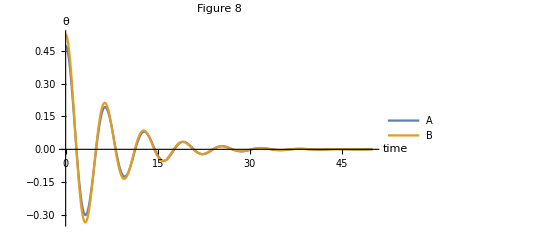

```mathematica
θBi = 3.14/6;θAi = 0.9*3.14/6;ωBi = 0;ωAi=0;
A = ImprovedCoupledDiffEqn1stOrderSolver[dθA, dθB, dωA, dωB ,θAi, θBi,ωAi,ωBi,t1,t2,stepsize];
ListLinePlot[ {A[[;;,{1,2}]],A[[;;,{1,3}]]}, PlotRange -> Full, AxesLabel -> {"time", "θ"},PlotLegends ->{"A","B"},PlotLabel -> "Figure 8"]
```

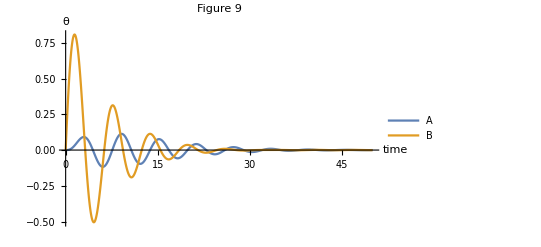

```mathematica
θBi = 0;θAi = 0;ωBi = 1;ωAi=0;
A = ImprovedCoupledDiffEqn1stOrderSolver[dθA, dθB, dωA, dωB ,θAi, θBi,ωAi,ωBi,t1,t2,stepsize];
ListLinePlot[ {A[[;;,{1,2}]],A[[;;,{1,3}]]}, PlotRange -> Full, AxesLabel -> {"time", "θ"},PlotLegends ->{"A","B"},PlotLabel -> "Figure 9"]
```

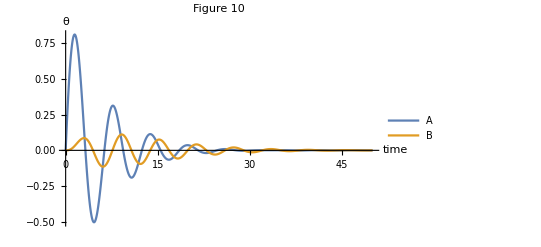

```mathematica
θBi = 0;θAi = 0;ωBi = 0;ωAi=1;
A = ImprovedCoupledDiffEqn1stOrderSolver[dθA, dθB, dωA, dωB ,θAi, θBi,ωAi,ωBi,t1,t2,stepsize];
ListLinePlot[ {A[[;;,{1,2}]],A[[;;,{1,3}]]}, PlotRange -> Full, AxesLabel -> {"time", "θ"},PlotLegends ->{"A","B"},PlotLabel -> "Figure 10"]
```